InterpolatingFunction[…]

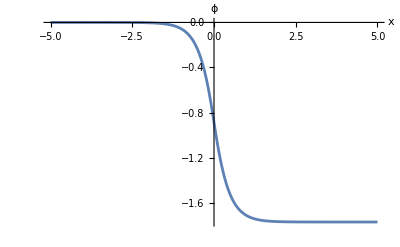

```mathematica
g=1.5;
κ=1;
(*This is the ground state wavefunction for the meson fluctuations around the steady state soliton, found by solving the linearized Schrodinger equation*)
ϕ0=Get["/home/zz3250/Wolfram Mathematica/BoundStateProfile"];
ϕ0 = Interpolation[ϕ0, InterpolationOrder->10]
Get["/home/zz3250/Wolfram Mathematica/SG_SS_Kappa1G1p5"];
PhiVSYKappa1G1p5=Interpolation[PhiVsYListKappa1G1p5,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa1G1p5[(π^(1/2)*Exp[(2 π*κ)^(1/2) x])/(1+Exp[(2 π*κ)^(1/2) x])]
Plot[ϕss[x],{x,-5,5},AxesLabel->{"x","ϕ"}]
(*Generate the table of values*)
data=Table[{x,ϕss[x]},{x,-100,100,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕss[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x] +g^2;
```

Eigensystem::maxit2: Warning: maximum number of iterations, 5000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

{1.79399,2.92145,2.92147,2.92233,2.92238,2.92379,2.9239,2.92583,2.92602,2.92846,2.92876,2.93167,2.93209,2.93546,2.93603,2.93984,2.94056,2.94479,2.94569,2.95032,2.95142,2.95643,2.95773,2.96311,2.96463,2.97036,2.97211,2.97818,2.98017,2.98657,2.98879,2.99551,2.99799,3.00501,3.00775,3.01506,3.01806,3.02566,3.02892,3.0368,3.04033,3.04847,3.05228,3.06068,3.06475,3.07341,3.07775,3.08665,3.09127,3.10041,3.1053,3.11467,3.11984,3.12943,3.13487,3.14468,3.15039,3.16042,3.16639,3.17663,3.18287,3.19331,3.19982,3.21045,3.21722,3.22805,3.23508,3.24609,3.25338,3.26458,3.27212,3.2835,3.29129,3.30284,3.31089,3.3226,3.33089,3.34278,3.35131,3.36335,3.37212,3.38432,3.39332,3.40568,3.41491,3.42742,3.43688,3.44954,3.45921,3.47202,3.48191,3.49486,3.50497,3.51805,3.52837,3.54159,3.55212,3.56546,3.5762,3.58967,3.6006,3.61421,3.62533,3.63906,3.65037,3.66422,3.67573,3.68969,3.70138,3.71546,3.72733,3.74152,3.75357,3.76787,3.78009,3.7945,3.80689,3.82141,3.83396,3.84858,3.86129,3.87602,3.88889,3.90371,3.91674,3.93166,3.94483,3.95986,3.97318,3.98829,4.00176,4.01696,4.03057,4.04587,4.05962,4.075,4.08888,4.10435,4.11837,4.13392,4.14807,4.1637,4.17797,4.19369,4.20809,4.22389,4.2384,4.25428,4.26891,4.28487}

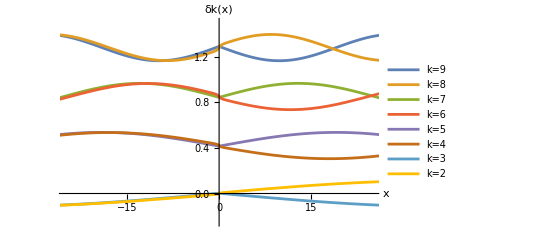

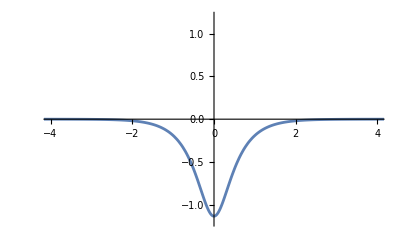

```mathematica
L=150;
total=150;
dx=.001;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->5000,"BasisSize"->total+1,"Shift"->3.2}];
Print[Sqrt[vals]]
Plot[{Evaluate[fns[[9]]+1.28],Evaluate[fns[[8]]+1.28],Evaluate[fns[[7]]+.85],Evaluate[-fns[[6]]+.85],Evaluate[fns[[5]]+.42],Evaluate[fns[[4]]+.42],Evaluate[fns[[3]]],Evaluate[fns[[2]]]},{x,-125,125},PlotRange->{{-25,25},{-.25,1.5}},AxesLabel->{"x","δk(x)"},PlotLegends->{"k=9","k=8","k=7","k=6","k=5","k=4","k=3","k=2"}]
Plot[Evaluate[fns[[1]]],{x,-5,5},PlotRange->{{-4,4},{-1.2,1.2}}]
```

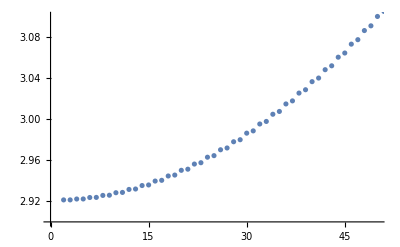

```mathematica
ListPlot[Sqrt[vals],PlotRange->{{0,50},{2.9,Sqrt[vals[[50]]]}}]
```

```mathematica
(*Choose incoming energies*)
k=187; (*this should always be an odd number/even fn*)
totalenergyin=Sqrt[vals[[1]]]+Sqrt[vals[[k]]];
acceptabledeltawidth=.05;
kout1={};
kout2={};
For[i=1,i<=total,i=i+2,
For[j=1,j<=total,j=j+2,
If[Abs[Sqrt[vals[[i]]]+Sqrt[vals[[j]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[kout1,i];AppendTo[kout2,j]];
];
];
```

```mathematica
Length[kout1]
Sqrt[vals[[k]]]
```

464

4.13834

```mathematica
outputenergydifference={};
matrixelement={};
For[i=1,i<=Length[kout1],i++,
dk[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2];
dk1[x_]:=(fns[[kout1[[i]]]]+I*fns[[kout1[[i]]-1]])/Sqrt[2];
dk2[x_]:=(fns[[kout2[[i]]]]+I*fns[[kout2[[i]]-1]])/Sqrt[2];
m=-(2*Pi)*Pi*Pi*κ/3*(1/(2*Sqrt[2]))*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*dk[x]*dk1[x]*dk2[x],{x,-L/2,L/2}];
diff=Sqrt[vals[[kout1[[i]]]]]-Sqrt[vals[[kout2[[i]]]]];
AppendTo[outputenergydifference,diff];
AppendTo[matrixelement,m];
Print[i]
];
```

$Aborted

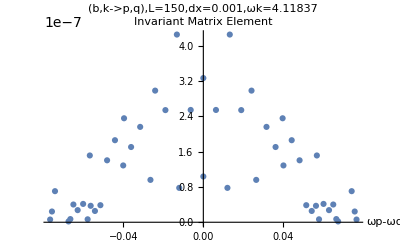

The mean is 1.22311×10^-7 and the SD is 1.12706×10^-7

```mathematica
sd=StandardDeviation[Abs[matrixelement]^2];
mean=Mean[Abs[matrixelement]^2];
plot=ListPlot[Transpose[{outputenergydifference,Abs[matrixelement]^2}],PlotLabel->Row@{"(b,k->p,q),L=",L,",dx=",dx,",ωk=",Sqrt[vals[[k]]]},AxesLabel->{"ωp-ωq","Invariant Matrix Element"}]
Print["The mean is ", mean, " and the SD is ", sd]
```

{50,100,150,200}

{2.11861×10^-6,5.15495×10^-7,1.86318×10^-7,6.16863×10^-8}

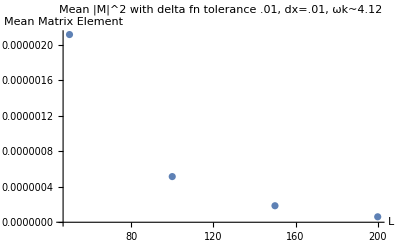

```mathematica
Llist={50,100,150,200}
meanlist={2.11861*10^(-6),5.15495*10^(-7),1.86318*10^(-7),6.16863*10^(-8)}
ListPlot[Transpose[{Llist,meanlist}],PlotLabel->"Mean |M|^2 with delta fn tolerance .01, dx=.01, ωk~4.12",AxesLabel->{"L","Mean Matrix Element"}]
```

Eigensystem::maxit2: Warning: maximum number of iterations, 5000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{1.79399,2.92124,2.92124,2.92146,2.92146,2.92183,2.92184,2.92235,2.92237,2.92301,2.92305,2.92383,2.92388,2.92479,2.92486,2.9259,2.92599,2.92715,2.92728,2.92856,2.92871,2.93011,2.93029,2.93181,2.93202,2.93366,2.9339,2.93565,2.93593,2.93779,2.93811,2.94008,2.94044,2.94251,2.94292,2.94509,2.94554,2.94781,2.94831,2.95068,2.95123,2.95369,2.95429,2.95685,2.9575,2.96015,2.96086,2.9636,2.96436,2.96719,2.96801,2.97092,2.97179,2.97479,2.97573,2.97881,2.9798,2.98297,2.98402,2.98726,2.98838,2.9917,2.99288,2.99628,2.99752,3.001,3.0023,3.00585,3.00722,3.01085,3.01228,3.01598,3.01748,3.02124,3.02281,3.02665,3.02828,3.03218,3.03388,3.03785,3.03962,3.04366,3.04549,3.0496,3.0515,3.05567,3.05764,3.06187,3.06391,3.0682,3.07031,3.07467,3.07684,3.08126,3.0835,3.08798,3.09029,3.09482,3.0972,3.1018,3.10424,3.1089,3.11141,3.11612,3.1187,3.12347,3.12612,3.13094,3.13366,3.13853,3.14132,3.14625,3.1491,3.15408,3.157,3.16204,3.16503,3.17011,3.17317,3.1783,3.18142,3.18661,3.1898,3.19504,3.19829,3.20358,3.20689,3.21223,3.21561,3.221,3.22445,3.22988,3.23339,3.23887,3.24244,3.24797,3.25161,3.25718,3.26088,3.2665,3.27027,3.27592,3.27976,3.28546,3.28935,3.2951,3.29905,3.30484,3.30886,3.31469,3.31877,3.32464,3.32878,3.3347,3.3389,3.34485,3.34911,3.35511,3.35942,3.36546,3.36984,3.37591,3.38035,3.38646,3.39096,3.39711,3.40166,3.40785,3.41246,3.41869,3.42336,3.42962,3.43435,3.44065,3.44543,3.45176,3.4566,3.46297,3.46786,3.47427,3.47921,3.48566,3.49065,3.49714,3.50218,3.5087,3.5138,3.52035,3.5255,3.53209,3.53729,3.54391,3.54917,3.55582,3.56112,3.56781,3.57317,3.57988,3.58529,3.59203,3.59749,3.60427,3.60978,3.61658,3.62214,3.62898,3.63458,3.64145,3.6471,3.654,3.6597,3.66663,3.67237,3.67933,3.68512,3.69211,3.69795,3.70497,3.71085,3.7179,3.72382,3.7309,3.73686,3.74397,3.74998,3.75711,3.76317,3.77033,3.77643,3.78361,3.78975,3.79697,3.80315,3.81039,3.81661,3.82388,3.83014,3.83743,3.84374,3.85106,3.8574,3.86475,3.87113,3.8785,3.88493,3.89232,3.89878,3.9062,3.9127,3.92015,3.92669,3.93415,3.94073,3.94822,3.95484,3.96235,3.969,3.97654,3.98323,3.99079,3.99752,4.0051,4.01186,4.01947,4.02626,4.03389,4.04072,4.04837,4.05527,4.06292}

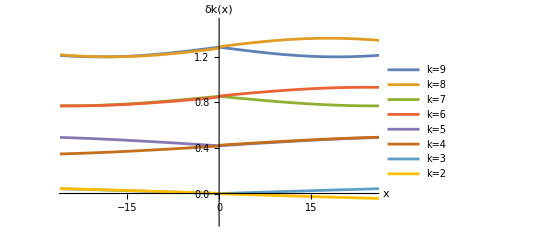

-Graphics-

```mathematica
(*2-level decay from bound state tree level*)
L=300;
total=270;
dx=.01;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->5000,"BasisSize"->total+1,"Shift"->3.2}];
Print[Sqrt[vals]]
Plot[{Evaluate[fns[[9]]+1.28],Evaluate[fns[[8]]+1.28],Evaluate[fns[[7]]+.85],Evaluate[-fns[[6]]+.85],Evaluate[fns[[5]]+.42],Evaluate[fns[[4]]+.42],Evaluate[fns[[3]]],Evaluate[fns[[2]]]},{x,-125,125},PlotRange->{{-25,25},{-.25,1.5}},AxesLabel->{"x","δk(x)"},PlotLegends->{"k=9","k=8","k=7","k=6","k=5","k=4","k=3","k=2"}]
Plot[Evaluate[fns[[1]]],{x,-5,5},PlotRange->{{-4,4},{-1.2,1.2}}]
```

```mathematica
(*Incoming energy is just 2ωb*)
totalenergyin=2*Sqrt[vals[[1]]]
acceptabledeltawidth=.1;
kout={};
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals[[i]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[kout,i]];
];
Length[kout]
Print[kout]
Print[Sqrt[vals[[kout]]]]
```

3.58797

17

{183,185,187,189,191,193,195,197,199,201,203,205,207,209,211,213,215}

{3.49065,3.50218,3.5138,3.5255,3.53729,3.54917,3.56112,3.57317,3.58529,3.59749,3.60978,3.62214,3.63458,3.6471,3.6597,3.67237,3.68512}

```mathematica
(*Decay rate for decay to the right*)
decayrate={};
For[i=1,i<=Length[kout],i++,
dkout[x_]:=(fns[[kout[[i]]]]+I*fns[[kout[[i]]-1]])/Sqrt[2];
m=-κ*8*Pi^(5/2)*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*fns[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[decayrate,m];
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0000236819+0.0252345 ⅈ and 7.1767×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000239527-0.0252912 ⅈ and 7.23107×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000242235-0.0253468 ⅈ and 7.28564×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

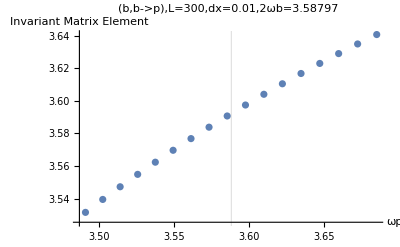

The mean is 3.58895 and the SD is 0.0344461

```mathematica
sd=StandardDeviation[Abs[decayrate]];
mean=Mean[Abs[decayrate]];
plot=ListPlot[Transpose[{Sqrt[vals[[kout]]],Abs[decayrate]}],PlotLabel->Row@{"(b,b->p),L=",L,",dx=",dx,",2ωb=",2*Sqrt[vals[[1]]]},AxesLabel->{"ωp","Invariant Matrix Element"},GridLines->{{2*Sqrt[vals[[1]]]},{}}]
Print["The mean is ", mean, " and the SD is ", sd]
```

```mathematica
(*Decay rate for decay to the left*)
decayrateleft={};
For[i=1,i<=Length[kout],i++,
dkout[x_]:=-(fns[[kout[[i]]]]-I*fns[[kout[[i]]-1]])/Sqrt[2];
m=-κ*8*Pi^(5/2)*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*fns[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[decayrateleft,m];
];
sd=StandardDeviation[Abs[decayrateleft]];
mean=Mean[Abs[decayrateleft]];
plot=ListPlot[Transpose[{Sqrt[vals[[kout]]],Abs[decayrateleft]}],PlotLabel->Row@{"(b,b->p),L=",L,",dx=",dx,",2ωb=",2*Sqrt[vals[[1]]]},AxesLabel->{"ωp","Invariant Matrix Element"},GridLines->{{2*Sqrt[vals[[1]]]},{}}]
Print["The mean is ", mean, " and the SD is ", sd]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained 0.0000236819+0.0252345 ⅈ and 7.1767×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0000239527-0.0252912 ⅈ and 7.23107×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0000242235-0.0253468 ⅈ and 7.28564×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

The mean is 3.58895 and the SD is 0.0344461

{50,100,150,200,250,300}

{17.4752,12.4316,10.1507,8.79094,7.86294,7.1779}

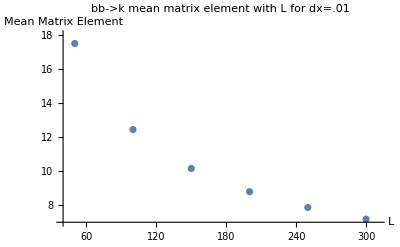

```mathematica
Llist={50,100,150,200,250,300}
decaylist=2*{8.7376,6.2158,5.07537,4.39547,3.93147,3.58895}
ListPlot[Transpose[{Llist,decaylist}],PlotLabel->"bb->k mean matrix element with L for dx=.01",AxesLabel->{"L","Mean Matrix Element"},PlotRange->{{40,310},{7,18}}]
```

Eigensystem::maxit2: Warning: maximum number of iterations, 5000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{1.79399,2.92133,2.92133,2.92182,2.92184,2.92265,2.9227,2.92381,2.92389,2.9253,2.92542,2.92711,2.92729,2.92926,2.92951,2.93174,2.93206,2.93455,2.93494,2.93768,2.93817,2.94115,2.94172,2.94494,2.94562,2.94905,2.94984,2.9535,2.9544,2.95826,2.95928,2.96335,2.96449,2.96877,2.97003,2.9745,2.9759,2.98055,2.98208,2.98691,2.98859,2.9936,2.99541,3.00059,3.00255,3.0079,3.01,3.01552,3.01777,3.02344,3.02584,3.03167,3.03422,3.0402,3.0429,3.04904,3.05189,3.05817,3.06117,3.06759,3.07075,3.07731,3.08062,3.08731,3.09078,3.09761,3.10123,3.10819,3.11196,3.11905,3.12297,3.13019,3.13426,3.1416,3.14583,3.15329,3.15767,3.16524,3.16977,3.17746,3.18215,3.18995,3.19478,3.2027,3.20768,3.2157,3.22083,3.22896,3.23423,3.24247,3.24789,3.25623,3.26179,3.27023,3.27594,3.28448,3.29032,3.29896,3.30494,3.31368,3.3198,3.32863,3.33489,3.34381,3.35021,3.35922,3.36575,3.37485,3.38151,3.3907,3.39749,3.40677,3.41369,3.42305,3.43009,3.43954,3.44671,3.45624,3.46353,3.47314,3.48056,3.49025,3.49779,3.50755,3.51521,3.52506,3.53283,3.54275,3.55064,3.56063,3.56864,3.5787,3.58682,3.59696,3.60519,3.6154,3.62373,3.63401,3.64246,3.6528,3.66135,3.67177,3.68042,3.6909,3.69966,3.71021,3.71907,3.72968,3.73864,3.74931,3.75837,3.7691,3.77825,3.78905,3.7983,3.80915,3.8185,3.82941,3.83885,3.84982,3.85935,3.87038,3.87999,3.89108,3.90078,3.91192,3.92171,3.93291,3.94278,3.95403,3.96399,3.97529,3.98533,3.99669,4.00681,4.01822,4.02841,4.03987,4.05015,4.06166,4.07201,4.08357,4.094,4.1056,4.11611,4.12776,4.13834,4.15004,4.16069,4.17243,4.18315,4.19494,4.20573,4.21757,4.22843,4.24031,4.25123,4.26316,4.27414,4.28611,4.29717,4.30918,4.32029,4.33235,4.34353,4.35562,4.36686,4.37899,4.3903,4.40247,4.41383,4.42604,4.43746,4.44971,4.46119,4.47348,4.48501,4.49734,4.50893,4.5213,4.53294,4.54534,4.55704,4.56948,4.58122,4.5937,4.6055,4.61801,4.62986,4.6424,4.65431,4.66688,4.67883,4.69145,4.70344,4.71609,4.72814,4.74081,4.75291,4.76562,4.77776,4.7905,4.80268,4.81545,4.82768,4.84049,4.85276,4.86559,4.87791,4.89078,4.90313,4.91603,4.92843,4.94135,4.95379,4.96674,4.97922,4.9922,5.00472,5.01773,5.03029,5.04333,5.05593,5.06899,5.08163,5.09472,5.10739,5.12051,5.13321,5.14636,5.1591,5.17227,5.18505,5.19825,5.21106,5.22428,5.23713,5.25038,5.26326,5.27653,5.28944,5.30274,5.31568,5.329,5.34198,5.35532,5.36833,5.3817,5.39474,5.40813,5.4212,5.43461,5.44771,5.46115,5.47428,5.48773,5.50089,5.51437,5.52756,5.54197}

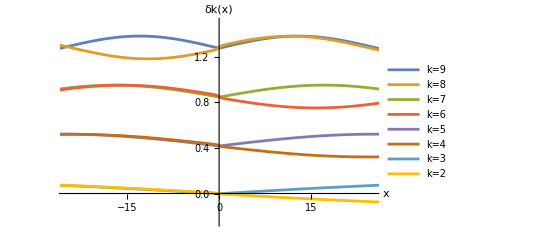

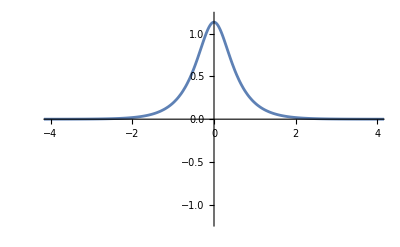

```mathematica
(*bk->p*)
L=200;
total=300;
dx=.01;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->5000,"BasisSize"->total+1,"Shift"->3.2}];
Print[Sqrt[vals]]
Plot[{Evaluate[fns[[9]]+1.28],Evaluate[fns[[8]]+1.28],Evaluate[fns[[7]]+.85],Evaluate[-fns[[6]]+.85],Evaluate[fns[[5]]+.42],Evaluate[fns[[4]]+.42],Evaluate[fns[[3]]],Evaluate[fns[[2]]]},{x,-125,125},PlotRange->{{-25,25},{-.25,1.5}},AxesLabel->{"x","δk(x)"},PlotLegends->{"k=9","k=8","k=7","k=6","k=5","k=4","k=3","k=2"}]
Plot[Evaluate[fns[[1]]],{x,-5,5},PlotRange->{{-4,4},{-1.2,1.2}}]
```

```mathematica
(*Incoming energy is ωb+ωk*)
k=3;
totalenergyin=Sqrt[vals[[1]]]+Sqrt[vals[[k]]]
acceptabledeltawidth=.05;
kout={};
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals[[i]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[kout,i]];
];
Length[kout]
Print[kout]
Print[Sqrt[vals[[kout]]]]
```

4.71532

4

{233,235,237,239}

{4.67883,4.70344,4.72814,4.75291}

```mathematica
matrixelement={};
For[i=1,i<=Length[kout],i++,
dkout[x_]:=(fns[[kout[[i]]]]+I*fns[[kout[[i]]-1]])/Sqrt[2];
dkin[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2];
m=-κ*(2/3)*Pi^(3/2)*(2*Pi)*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*dkin[x]*dkout[x],{x,-L/2,L/2}];
AppendTo[matrixelement,m];
];
```

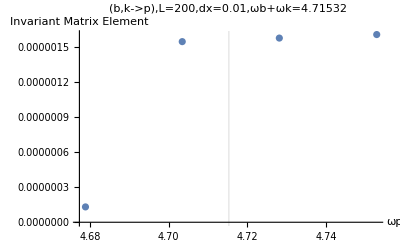

```mathematica
plot=ListPlot[Transpose[{Sqrt[vals[[kout]]],Abs[matrixelement]^2}],PlotLabel->Row@{"(b,k->p),L=",L,",dx=",dx,",ωb+ωk=",Sqrt[vals[[1]]]+Sqrt[vals[[k]]]},AxesLabel->{"ωp","Invariant Matrix Element"},GridLines->{{Sqrt[vals[[1]]]+Sqrt[vals[[k]]]},{}}]
```

```mathematica
(*bbk->p*)
L=200;
total=400;
dx=.01;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->5000,"BasisSize"->total+1,"Shift"->3.2}];
Print[Sqrt[vals]]
Plot[{Evaluate[fns[[9]]+1.28],Evaluate[fns[[8]]+1.28],Evaluate[fns[[7]]+.85],Evaluate[-fns[[6]]+.85],Evaluate[fns[[5]]+.42],Evaluate[fns[[4]]+.42],Evaluate[fns[[3]]],Evaluate[fns[[2]]]},{x,-125,125},PlotRange->{{-25,25},{-.25,1.5}},AxesLabel->{"x","δk(x)"},PlotLegends->{"k=9","k=8","k=7","k=6","k=5","k=4","k=3","k=2"}]
Plot[Evaluate[fns[[1]]],{x,-5,5},PlotRange->{{-4,4},{-1.2,1.2}}]
```

Eigensystem::maxit2: Warning: maximum number of iterations, 5000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{1.79399,2.92133,2.92133,2.92182,2.92184,2.92265,2.9227,2.92381,2.92389,2.9253,2.92542,2.92711,2.92729,2.92926,2.92951,2.93174,2.93206,2.93455,2.93494,2.93768,2.93817,2.94115,2.94172,2.94494,2.94562,2.94905,2.94984,2.9535,2.9544,2.95826,2.95928,2.96335,2.96449,2.96877,2.97003,2.9745,2.9759,2.98055,2.98208,2.98691,2.98859,2.9936,2.99541,3.00059,3.00255,3.0079,3.01,3.01552,3.01777,3.02344,3.02584,3.03167,3.03422,3.0402,3.0429,3.04904,3.05189,3.05817,3.06117,3.06759,3.07075,3.07731,3.08062,3.08731,3.09078,3.09761,3.10123,3.10819,3.11196,3.11905,3.12297,3.13019,3.13426,3.1416,3.14583,3.15329,3.15767,3.16524,3.16977,3.17746,3.18215,3.18995,3.19478,3.2027,3.20768,3.2157,3.22083,3.22896,3.23423,3.24247,3.24789,3.25623,3.26179,3.27023,3.27594,3.28448,3.29032,3.29896,3.30494,3.31368,3.3198,3.32863,3.33489,3.34381,3.35021,3.35922,3.36575,3.37485,3.38151,3.3907,3.39749,3.40677,3.41369,3.42305,3.43009,3.43954,3.44671,3.45624,3.46353,3.47314,3.48056,3.49025,3.49779,3.50755,3.51521,3.52506,3.53283,3.54275,3.55064,3.56063,3.56864,3.5787,3.58682,3.59696,3.60519,3.6154,3.62373,3.63401,3.64246,3.6528,3.66135,3.67177,3.68042,3.6909,3.69966,3.71021,3.71907,3.72968,3.73864,3.74931,3.75837,3.7691,3.77825,3.78905,3.7983,3.80915,3.8185,3.82941,3.83885,3.84982,3.85935,3.87038,3.87999,3.89108,3.90078,3.91192,3.92171,3.93291,3.94278,3.95403,3.96399,3.97529,3.98533,3.99669,4.00681,4.01822,4.02841,4.03987,4.05015,4.06166,4.07201,4.08357,4.094,4.1056,4.11611,4.12776,4.13834,4.15004,4.16069,4.17243,4.18315,4.19494,4.20573,4.21757,4.22843,4.24031,4.25123,4.26316,4.27414,4.28611,4.29717,4.30918,4.32029,4.33235,4.34353,4.35562,4.36686,4.37899,4.3903,4.40247,4.41383,4.42604,4.43746,4.44971,4.46119,4.47348,4.48501,4.49734,4.50893,4.5213,4.53294,4.54534,4.55704,4.56948,4.58122,4.5937,4.6055,4.61801,4.62986,4.6424,4.65431,4.66688,4.67883,4.69145,4.70344,4.71609,4.72814,4.74081,4.75291,4.76562,4.77776,4.7905,4.80268,4.81545,4.82768,4.84049,4.85276,4.86559,4.87791,4.89078,4.90313,4.91603,4.92843,4.94135,4.95379,4.96674,4.97922,4.9922,5.00472,5.01773,5.03029,5.04333,5.05593,5.06899,5.08163,5.09472,5.10739,5.12051,5.13321,5.14636,5.1591,5.17227,5.18505,5.19825,5.21106,5.22428,5.23713,5.25038,5.26326,5.27653,5.28944,5.30274,5.31568,5.329,5.34198,5.35532,5.36833,5.3817,5.39474,5.40813,5.4212,5.43461,5.44771,5.46115,5.47428,5.48773,5.50089,5.51437,5.52756,5.54106,5.55428,5.5678,5.58104,5.59458,5.60785,5.62142,5.63472,5.6483,5.66162,5.67523,5.68858,5.7022,5.71558,5.72922,5.74262,5.75628,5.76971,5.78339,5.79684,5.81054,5.82402,5.83774,5.85124,5.86497,5.8785,5.89225,5.9058,5.91957,5.93314,5.94693,5.96052,5.97433,5.98795,6.00177,6.01541,6.02925,6.04291,6.05677,6.07045,6.08432,6.09802,6.11191,6.12563,6.13954,6.15328,6.16721,6.18097,6.19491,6.20869,6.22264,6.23644,6.25041,6.26423,6.27822,6.29206,6.30606,6.31991,6.33393,6.3478,6.36184,6.37573,6.38978,6.40368,6.41775,6.43167,6.44575,6.45969,6.47378,6.48774,6.50185,6.51582,6.52994,6.54394,6.55807,6.57208,6.58622,6.60025,6.61441,6.62845,6.64262,6.65668,6.67086,6.68494,6.69914,6.71322,6.72743,6.74154,6.75576,6.76988,6.78411,6.79825,6.81249,6.82664,6.8409,6.85506,6.86933,6.88351,6.8978,6.92551,6.93049}

-Graphics-

-Graphics-

```mathematica
k=3;
totalenergyin=2*Sqrt[vals[[1]]]+Sqrt[vals[[k]]]
acceptabledeltawidth=.1;
kout={};
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals[[i]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[kout,i]];
];
Length[kout]
Print[kout]
Print[Sqrt[vals[[kout]]]]
```

6.5093

7

{365,367,369,371,373,375,377}

{6.43167,6.45969,6.48774,6.51582,6.54394,6.57208,6.60025}

```mathematica
matrixelement={};
For[i=1,i<=Length[kout],i++,
dkout[x_]:=(fns[[kout[[i]]]]+I*fns[[kout[[i]]-1]])/Sqrt[2];
dkin[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2];
m=-κ*(1/3)*Pi^2*(2*Pi)*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*fns[[1]]*dkin[x]*dkout[x],{x,-L/2,L/2}];
AppendTo[matrixelement,m];
];
```

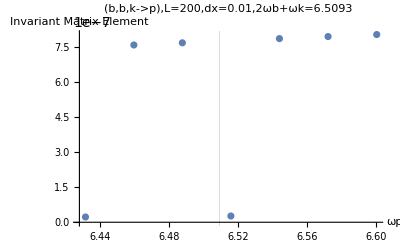

```mathematica
plot=ListPlot[Transpose[{Sqrt[vals[[kout]]],Abs[matrixelement]^2}],PlotLabel->Row@{"(b,b,k->p),L=",L,",dx=",dx,",2ωb+ωk=",2*Sqrt[vals[[1]]]+Sqrt[vals[[k]]]},AxesLabel->{"ωp","Invariant Matrix Element"},GridLines->{{2*Sqrt[vals[[1]]]+Sqrt[vals[[k]]]},{}}]
```

```mathematica
(*bbk->pq*)
k=3;
totalenergyin=2*Sqrt[vals[[1]]]+Sqrt[vals[[k]]]
acceptabledeltawidth=.01;
kout1={};
kout2={};
For[i=3,i<=total,i=i+2,
For[j=3,j<=total,j=j+2,
If[Abs[Sqrt[vals[[i]]]+Sqrt[vals[[j]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[kout1,i];AppendTo[kout2,j]];
];
];
Length[kout1]
Print[kout1]
Print[Sqrt[vals[[kout1]]]]
```

```mathematica
outputenergydifference={};
matrixelement={};
For[i=1,i<=Length[kout1],i++,
dk[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2];
dk1[x_]:=(fns[[kout1[[i]]]]+I*fns[[kout1[[i]]-1]])/Sqrt[2];
dk2[x_]:=(fns[[kout2[[i]]]]+I*fns[[kout2[[i]]-1]])/Sqrt[2];
m=-(2*Pi)*Pi*Pi*κ/3*(1/(2*Sqrt[2]))*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*dk[x]*dk1[x]*dk2[x],{x,-L/2,L/2}];
diff=Sqrt[vals[[kout1[[i]]]]]-Sqrt[vals[[kout2[[i]]]]];
AppendTo[outputenergydifference,diff];
AppendTo[matrixelement,m];
];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 5000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{0.357754,2.52463,2.52471,2.52505,2.5253,2.52584,2.52629,2.52703,2.52767,2.5286,2.52944,2.53057,2.5316,2.53293,2.53415,2.53568,2.5371,2.53881,2.54043,2.54234,2.54415,2.54625,2.54825,2.55054,2.55273,2.55522,2.5576,2.56027,2.56285,2.5657,2.56847,2.57151,2.57446,2.57769,2.58083,2.58425,2.58757,2.59116,2.59467,2.59845,2.60213,2.60609,2.60996,2.61409,2.61814,2.62245,2.62667,2.63116,2.63555,2.64021,2.64478,2.64961,2.65435,2.65935,2.66426,2.66942,2.67451,2.67983,2.68508,2.69057,2.69598,2.70163,2.70721,2.71302,2.71875,2.72472,2.73061,2.73673,2.74278,2.74905,2.75526,2.76168,2.76803,2.7746,2.78111,2.78783,2.79448,2.80134,2.80814,2.81514,2.82208,2.82923,2.83631,2.84359,2.85081,2.85823,2.86559,2.87314,2.88064,2.88832,2.89594,2.90375,2.91151,2.91945,2.92734,2.9354,2.94341,2.9516,2.95974,2.96804,2.97631,2.98473,2.99311,3.00165,3.01015,3.01881,3.02743,3.0362,3.04493,3.05381,3.06265,3.07164,3.0806,3.0897,3.09876,3.10796,3.11713,3.12644,3.13571,3.14512,3.15449,3.164,3.17348,3.18309,3.19266,3.20236,3.21204,3.22183,3.2316,3.24149,3.25136,3.26134,3.27129,3.28136,3.29141,3.30157,3.3117,3.32195,3.33217,3.3425,3.3528,3.36322,3.37361,3.3841,3.39458,3.40515,3.4157,3.42636,3.43699,3.44772,3.45843,3.46924,3.48003,3.49091,3.50177,3.51272,3.52366,3.53468,3.54569,3.55679,3.56786,3.57903,3.59018,3.60141,3.61263,3.62392,3.63521,3.64657,3.65792,3.66935,3.68076,3.69225,3.70373,3.71528,3.72682,3.73843,3.75003,3.7617,3.77336,3.78509,3.79681,3.8086,3.82038,3.83222,3.84405,3.85595,3.86784,3.87979,3.89174,3.90374,3.91574,3.92779,3.93984,3.95195,3.96405,3.97621,3.98836,4.00057,4.01277,4.02503,4.03728,4.04958,4.06188,4.07423,4.08658,4.09897,4.11136,4.12381,4.13624,4.14873,4.16121,4.17374,4.18626,4.19883,4.2114,4.22401,4.23662,4.24928,4.26193,4.27462,4.28732,4.30005,4.31278,4.32556,4.33833,4.35114,4.36395,4.3768,4.38965,4.40253,4.41542,4.42834,4.44126,4.45422,4.46718,4.48017,4.49316,4.50619,4.51922,4.53228,4.54534,4.55843,4.57153,4.58466,4.59778,4.61094,4.6241,4.6373,4.65049,4.66371,4.67693,4.69019,4.70344,4.71672,4.73001,4.74332,4.75663,4.76998,4.78332,4.79669,4.81006,4.82346,4.83686,4.85029,4.86371,4.87717,4.89062,4.9041,4.91758,4.93109,4.9446,4.95813,4.97166,4.98522,4.99878,5.01236,5.02595,5.03955,5.05316,5.0668,5.08043,5.09408,5.10774,5.12142,5.1351,5.1488,5.16251,5.17623,5.18996,5.20371,5.21746,5.23123,5.245,5.25879,5.27258,5.28639,5.30021,5.31404,5.32788,5.34173,5.35559,5.36946,5.38334,5.39723,5.41113,5.42504,5.43896,5.45289,5.46683,5.48078,5.49474,5.50871,5.52268,5.53667,5.55067,5.56468,5.57869,5.59271,5.60674,5.62079,5.63483,5.6489,5.66296,5.67704,5.69112,5.70522,5.71931,5.73343,5.74754,5.76167,5.7758,5.78995,5.8041,5.81826,5.83242,5.8466,5.86078,5.87497,5.88917,5.90338,5.91759,5.93181,5.94604,5.96027,5.97451,5.98877,6.00302,6.01729,6.03156,6.04584,6.06012,6.07442,6.08872,6.10303,6.11734,6.13166,6.14599,6.16032,6.17466,6.18901,6.20337,6.21773,6.23209,6.24647,6.26085,6.27524,6.28963,6.30403,6.31843,6.33285,6.34726,6.36169,6.37612,6.39056,6.405,6.41945,6.4339,6.44836,6.46282,6.4773,6.49177,6.50626,6.52074,6.53524,6.54974,6.56425,6.57875,6.59327,6.60779,6.62232,6.63685,6.65139,6.66593,6.68048,6.69504,6.7096,6.72416,6.73873,6.75331,6.76789,6.78247,6.79706,6.81165,6.82625,6.84086,6.85547,6.87008,6.8847,6.89932,6.91395,6.92859,6.94323,6.95787,6.97252,6.98717,7.00182,7.01648,7.03115,7.04582,7.0605,7.07517,7.08986,7.10455,7.11924,7.13393,7.14864,7.16334,7.17805,7.19276,7.20748,7.2222,7.23693,7.25166,7.2664,7.28113,7.29588,7.31062,7.32537,7.34013,7.35489,7.36965,7.38442,7.39918,7.41396,7.42874,7.44352,7.4583,7.47309,7.48789,7.50268,7.51748,7.53229,7.5471,7.56191,7.57672,7.59154,7.60636,7.62119,7.63602,7.65085,7.66569,7.68053,7.69537,7.71022,7.72507,7.73992,7.75478,7.76964,7.7845,7.79937,7.81424,7.82911,7.84399,7.85887,7.87375,7.88864,7.90353,7.91842,7.93331,7.94821,7.96311,7.97802,7.99293,8.00784,8.02275,8.03767,8.05259,8.06751,8.08244,8.09737,8.1123,8.12724,8.14227,8.16212,8.17402,8.18835,8.20344,8.2199,8.24946,8.26502}

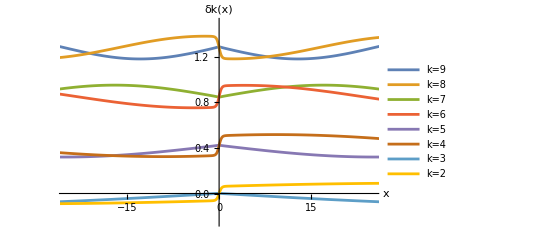

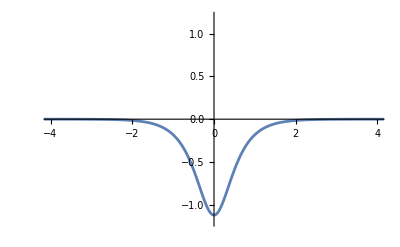

```mathematica
(*First order processes compilation*)
L=200;
total=500;
dx=.01;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->5000,"BasisSize"->total+1,"Shift"->3.2}];
Print[Sqrt[vals]]
Plot[{Evaluate[fns[[9]]+1.28],Evaluate[fns[[8]]+1.28],Evaluate[fns[[7]]+.85],Evaluate[-fns[[6]]+.85],Evaluate[fns[[5]]+.42],Evaluate[fns[[4]]+.42],Evaluate[fns[[3]]],Evaluate[fns[[2]]]},{x,-125,125},PlotRange->{{-25,25},{-.25,1.5}},AxesLabel->{"x","δk(x)"},PlotLegends->{"k=9","k=8","k=7","k=6","k=5","k=4","k=3","k=2"}]
Plot[Evaluate[fns[[1]]],{x,-5,5},PlotRange->{{-4,4},{-1.2,1.2}}]
```

```mathematica
acceptabledeltawidth=.05;
k=283;
Sqrt[vals[[k]]]
```

5.10774

```mathematica
(*Processess that occurr at first order with 1-2 b are
1. Decay bb->p
2. bk->p
3. bk->pq
4. bbk->p
*)
(*First we calculate the decay rate*)
totalenergyin=2*Sqrt[vals[[1]]];
acceptabledeltawidth=.05;
Poutbbtop={};
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals[[i]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[Poutbbtop,i]];
];
Length[Poutbbtop]
Print[Poutbbtop]
Print[Sqrt[vals[[Poutbbtop]]]]
bbtop={};
For[i=1,i<=Length[Poutbbtop],i++,
dkout[x_]:=(fns[[Poutbbtop[[i]]]]+I*fns[[Poutbbtop[[i]]-1]])/Sqrt[2];
m=-3*2*κ*(2*Pi)*(2/3)*Pi^(3/2)*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*fns[[1]]*dkout[x],{x,-L/2,L/2}];
AppendTo[bbtop,Abs[m]^2];
];
```

0

{}

{}

```mathematica
(*Next we calculate bk->p*)
totalenergyin=Sqrt[vals[[1]]]+Sqrt[vals[[k]]]
Poutbktop={};
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals[[i]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[Poutbktop,i]];
];
Length[Poutbktop]
Print[Poutbktop]
Print[Sqrt[vals[[Poutbktop]]]]
bktop={};
For[i=1,i<=Length[Poutbktop],i++,
dkout[x_]:=(fns[[Poutbktop[[i]]]]+I*fns[[Poutbktop[[i]]-1]])/Sqrt[2];
dkin[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2];
m=-κ*3*2*(2/3)*Pi^(3/2)*(2*Pi)*NIntegrate[Sin[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*dkin[x]*dkout[x],{x,-L/2,L/2}];
AppendTo[bktop,Abs[m]^2];
];
```

5.4655

3

{307,309,311}

{5.43896,5.46683,5.49474}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained 1.64686×10^-8+0.0000184687 ⅈ and 2.94474×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained 1.64386×10^-8+0.0000185468 ⅈ and 2.99071×10^-7 for the integral and error estimates.

```mathematica
(*bk->pq*)
acceptabledeltawidth=.01
totalenergyin=Sqrt[vals[[1]]]+Sqrt[vals[[k]]];
Poutbkpq={};
Qoutbkpq={};
For[i=3,i<=total,i=i+2,
For[j=3,j<=total,j=j+2,
If[Abs[Sqrt[vals[[i]]]+Sqrt[vals[[j]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[Poutbkpq,i];AppendTo[Qoutbkpq,j]];
];
];
Length[Poutbkpq]
bktopq={};
For[i=1,i<=Length[Poutbkpq],i++,
dk[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2];
dk1[x_]:=(fns[[Poutbkpq[[i]]]]+I*fns[[Poutbkpq[[i]]-1]])/Sqrt[2];
dk2[x_]:=(fns[[Qoutbkpq[[i]]]]+I*fns[[Qoutbkpq[[i]]-1]])/Sqrt[2];
m=-4*3*2*(2*Pi)*Pi*Pi*κ/3*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*dk[x]*dk1[x]*dk2[x],{x,-L/2,L/2}];
AppendTo[bktopq,Abs[m]^2];
];
Print[bktopq]
```

0.01

87

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained -0.0000467422-1.33966×10^-9 ⅈ and 8.46648×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained -0.0000648476-1.83942×10^-9 ⅈ and 1.15068×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained 0.0000703956+1.96988×10^-9 ⅈ and 1.21821×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.000537722,0.00103497,0.00121964,0.00126692,0.00126158,0.00129751,0.00132194,0.00135689,0.00128462,0.00135116,0.00136233,0.00133844,0.00137256,0.00134838,0.00135816,0.00136796,0.00134518,0.00137788,0.00135554,0.00136617,0.000505408,0.000193237,0.00133882,0.000536357,0.00135132,0.000184544,0.000180233,0.00108099,0.00132179,0.00134907,0.00104764,0.000172069,0.000171073,0.000168343,0.000170244,0.000167453,0.000740385,0.000764712,0.00078968,0.000787764,0.000868623,0.000162514,0.000165431,0.000866975,0.000868623,0.000866975,0.00078968,0.000162514,0.000764712,0.000787764,0.000170244,0.000740385,0.000171073,0.000167453,0.000172069,0.000168343,0.00132179,0.00104764,0.00108099,0.00134907,0.000184544,0.000180233,0.00133882,0.00135132,0.000505408,0.000193237,0.000536357,0.00134518,0.00135554,0.00136617,0.00133844,0.00134838,0.00135816,0.00136796,0.00137788,0.00126158,0.00132194,0.00128462,0.00135116,0.00136233,0.00137256,0.000537722,0.00103497,0.00121964,0.00126692,0.00129751,0.00135689}

```mathematica
(*bbk->p*)
acceptabledeltawidth=.05;
totalenergyin=2*Sqrt[vals[[1]]]+Sqrt[vals[[k]]]
Poutbbktop={};
For[i=3,i<=total,i=i+2,
If[Abs[Sqrt[vals[[i]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[Poutbbktop,i]];
];
Length[Poutbbktop]
Print[Poutbbktop]
Print[Sqrt[vals[[Poutbbktop]]]]
bbktop={};
For[i=1,i<=Length[Poutbbktop],i++,
dkout[x_]:=(fns[[Poutbbktop[[i]]]]+I*fns[[Poutbbktop[[i]]-1]])/Sqrt[2];
dkin[x_]:=(fns[[k]]+I*fns[[k-1]])/Sqrt[2];
m=-4*3*2*κ*(1/3)*Pi^2*(2*Pi)*NIntegrate[Cos[2*Sqrt[Pi]*ϕssint[x]]*fns[[1]]*fns[[1]]*dkin[x]*dkout[x],{x,-L/2,L/2}];
AppendTo[bbktop,Abs[m]^2];
];
```

5.82325

4

{331,333,335,337}

{5.7758,5.8041,5.83242,5.86078}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained -0.000156629-3.24546×10^-8 ⅈ and 6.59132×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained -0.00128803+1.04915×10^-8 ⅈ and 2.16051×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00310833}. NIntegrate obtained -0.00129591+1.09818×10^-8 ⅈ and 2.20523×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
(*bb->p graph*)
ListPlot[Transpose[{Sqrt[vals[[Poutbbtop]]],bbtop}]]
```

-Graphics-

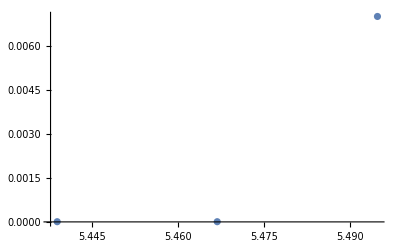

```mathematica
(*bk->p graph*)
ListPlot[Transpose[{Sqrt[vals[[Poutbktop]]],bktop}]]
```

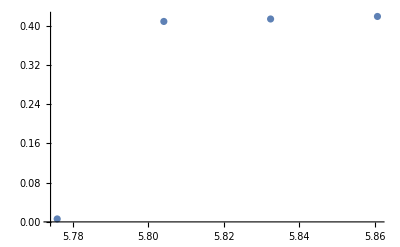

```mathematica
(*bbk->p graph*)
ListPlot[Transpose[{Sqrt[vals[[Poutbbktop]]],bbktop}]]
```

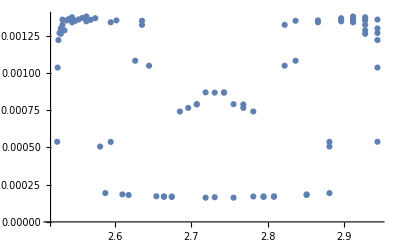

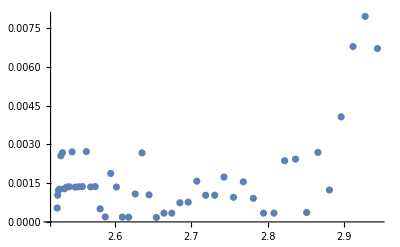

```mathematica
grouped=GroupBy[Transpose[{Poutbkpq,bktopq}],First->Last,Total];
bkpqenergy=Keys[grouped];
bkpqmatrixelement=Values[grouped];
ListPlot[Transpose[{Sqrt[vals[[Poutbkpq]]],bktopq}]]
ListPlot[Transpose[{Sqrt[vals[[bkpqenergy]]],bkpqmatrixelement}]]
```

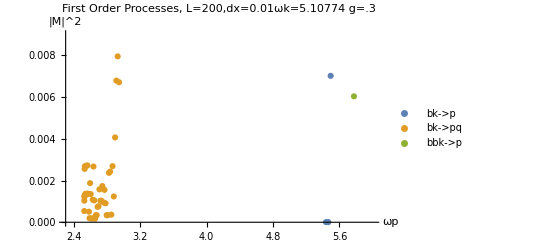

```mathematica
(*All together*)
ListPlot[{Transpose[{Sqrt[vals[[Poutbktop]]],bktop}],Transpose[{Sqrt[vals[[bkpqenergy]]],bkpqmatrixelement}],Transpose[{Sqrt[vals[[Poutbbktop]]],bbktop}]},PlotLegends->{"bk->p","bk->pq","bbk->p"},PlotLabel->Row@{"First Order Processes, L=",L,",dx=",dx,"ωk=",Sqrt[vals[[k]]]," g=.3"},AxesLabel->{"ωp","|M|^2"},PlotRange->{{2.3,6},{0,.009}}]
```

```mathematica
Print[Poutbkpq]
```

{1,3,3,3,3,5,5,5,5,7,7,7,9,9,9,9,11,11,11,11,13,13,13,13,15,15,15,15,17,17,17,17,19,19,19,19,21,21,21,21,21,23,23,23,23,23,25,25,25,25,25,27,27,27,27,27,27,29,29,29,29,29,29,29,29,31,31,31,31,31,31,31,31,31,31,33,33,33,33,33,33,33,33,35,35,35,35,35,35,37,37,183}

```mathematica
Sqrt[vals[[3]]]+Sqrt[vals[[37]]]
Sqrt[vals[[3]]]
Sqrt[vals[[37]]]
```

5.89723

2.92133

2.9759

```mathematica
acceptabledeltawidth=.1
totalenergyin=Sqrt[vals[[1]]]+Sqrt[vals[[k]]];
Poutbkpqtest={};
Qoutbkpqtest={};
For[i=3,i<=total,i=i+2,
For[j=3,j<=total,j=j+2,
If[Abs[Sqrt[vals[[i]]]+Sqrt[vals[[j]]]-totalenergyin]<=acceptabledeltawidth,AppendTo[Poutbkpq,i];AppendTo[Qoutbkpq,j]];
];
];
Length[Poutbkpq]
Print[Poutbkpq]
```

0.1

746

{1,3,3,3,3,5,5,5,5,7,7,7,9,9,9,9,11,11,11,11,13,13,13,13,15,15,15,15,17,17,17,17,19,19,19,19,21,21,21,21,21,23,23,23,23,23,25,25,25,25,25,27,27,27,27,27,27,29,29,29,29,29,29,29,29,31,31,31,31,31,31,31,31,31,31,33,33,33,33,33,33,33,33,35,35,35,35,35,35,37,37,183,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,53,53,53,53,53,53,53,53,53,53,53,53,53,55,55,55,55,55,55,55,55,55,55,55,57,57,57,57,57,57,57,57,57,59,59,59,59,59}

```mathematica
Sqrt[vals[[59]]]
```

3.06117